```mathematica
P[T_,μB_]:=c(T0/ℏc)^4((T/T0)^2+(μB/μB0)^2)^2;
s[T_,μB_]:=ℏc D[P[T,μB],T];
ρB[T_,μB_]:=ℏc D[P[T,μB],μB];
P[T,μB]//FullSimplify
-P[T,μB]+(T s[T,μB]+μB ρB[T,μB])/ℏc//FullSimplify
```

(c (T0^2 μB^2+T^2 μB0^2)^2)/(μB0^4 ℏc^4)

(3 c (T0^2 μB^2+T^2 μB0^2)^2)/(μB0^4 ℏc^4)

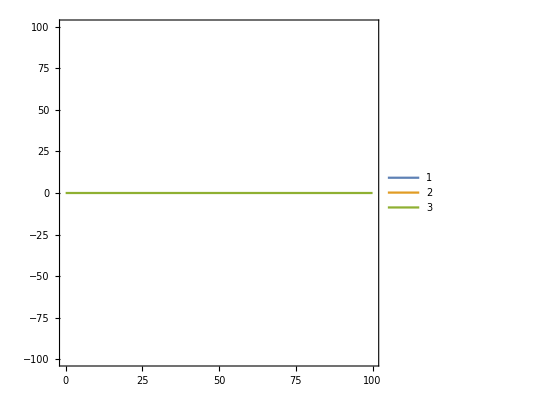

```mathematica
ContourPlot[{-P[T,μB]+(T s[T,μB]+μB ρB[T,μB])/ℏc,s[T,μB],ρB[T,μB]}/.{ℏc->197.3,c->4,T0->1,μB0->1}//Evaluate,{T,0,100},{μB,-100,100},PlotLegends->Automatic]
```

```mathematica
Plot3D[(2x y)/(1+x^2+y^2),{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Flatten[Table[{r Cos[ϕ],r Sin[ϕ]},{r,1/10,10,1/10},{ϕ,0,2π,(2π)/1000}],1]//Length
```

100100